This file is not published.
Run the file Solver N=2* SYM analytic first.

```mathematica
ResourceFunction["MaTeXInstall"][];
<<MaTeX`

defaultplotstyle=("DefaultPlotStyle"/. (Method/.Charting`ResolvePlotTheme[Automatic,Plot]));
```

## Root and ratio test - small M

```mathematica
tmp=Table[0,{ll,cutoffλ}];
tmp2=solution/.{Derivative[n_][γ][0]:>γExpl[n]};
SetSharedVariable[tmp];
ParallelTable[{
Print[" Expand order λ: ",ll,"/",cutoffλ];
tmp[[ll]]=Series[Wλ[1,ll]/.tmp2,{M,0,10}]//FunctionExpand;
},{ll,cutoffλ},Method->"FinestGrained"];
```

Expand order λ: 1/35

Expand order λ: 2/35

Expand order λ: 3/35

Expand order λ: 4/35

Expand order λ: 5/35

Expand order λ: 6/35

Expand order λ: 7/35

Expand order λ: 8/35

Expand order λ: 9/35

Expand order λ: 10/35

Expand order λ: 11/35

Expand order λ: 12/35

Expand order λ: 13/35

Expand order λ: 14/35

Expand order λ: 15/35

Expand order λ: 16/35

Expand order λ: 17/35

Expand order λ: 18/35

Expand order λ: 19/35

Expand order λ: 20/35

Expand order λ: 21/35

Expand order λ: 22/35

Expand order λ: 23/35

Expand order λ: 24/35

Expand order λ: 25/35

Expand order λ: 26/35

Expand order λ: 27/35

Expand order λ: 28/35

Expand order λ: 29/35

Expand order λ: 30/35

Expand order λ: 31/35

Expand order λ: 32/35

Expand order λ: 33/35

Expand order λ: 34/35

Expand order λ: 35/35

```mathematica
(* odd powers of M *)
Table[SeriesCoefficient[tmp,{M,0,m}],{m,1,9,2}]//Flatten//Union
```

{0}

Signs and intercepts in units of λ/π^2

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

-0.0101628

{0,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1}

0.9675

{0,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1}

1.02636

{0,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1}

1.06951

{0,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1}

1.10048

{0,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1}

1.121

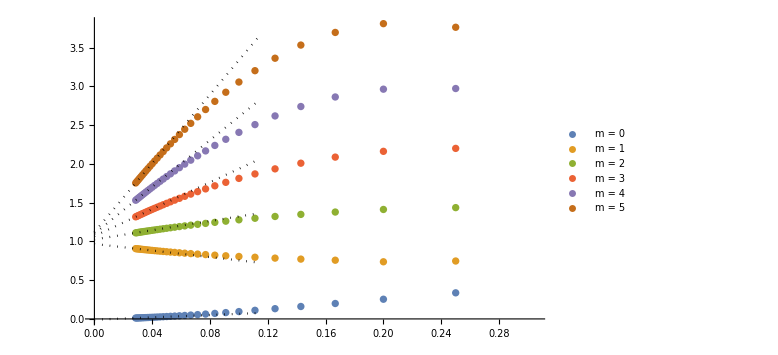

Intercepts in units of λ/π^2

-0.00201362

-0.999147

-1.00046

-0.998022

-0.99216

-0.983022

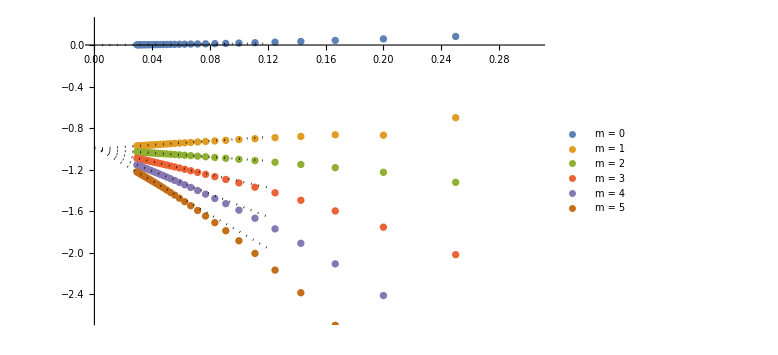

```mathematica
(* even powers of M *)
Print["Signs and intercepts in units of λ/π^2"]
For[m=0,m<=10,m=m+2,{
tmp3=SeriesCoefficient[tmp,{M,0,m}];
Print[Sign[tmp3]//Round];
tmp3=Table[{1/ll,π^2 Abs[tmp3[[ll]]]^(1/ll)},{ll,Length[tmp3]}];
points[m]=tmp3;
line[m]=Fit[tmp3[[-5;;-1]],{1,x},x];
Print[line[m]/.x->0];
}];

ListPlot[Evaluate@Table[points[m],{m,0,10,2}],AxesLabel->{MaTeX["1/\\ell"],MaTeX["\\frac{1}{16} \\left| \\mathbb{W}_{\\ell,m}(2\\pi) \\right|^{1/\ell}"],Black},PlotStyle->defaultplotstyle,PlotLegends->Table[Row[{"m = ",m}],{m,0,5}],ImageSize->Large];
Plot[Table[line[m],{m,0,10,2}],{x,0,4/Length[tmp3]},PlotStyle->{Black,Dotted},ImageSize->Large];
Show[%%,%]

Print["Intercepts in units of λ/π^2"]
For[m=0,m<=10,m=m+2,{
tmp3=SeriesCoefficient[tmp,{M,0,m}];
tmp3=Table[{1/ll,π^2 tmp3[[ll+1]]/tmp3[[ll]]},{ll,2,Length[tmp3]-1}];
points[m]=tmp3;
line[m]=Fit[tmp3[[-5;;-1]],{1,x},x];
Print[line[m]/.x->0];
}];

ListPlot[Evaluate@Table[points[m],{m,0,10,2}],AxesLabel->{MaTeX["1/\\ell"],MaTeX["\\frac{1}{16} \\frac{\\mathbb{W}_{\\ell+1,m}(2\\pi)}{\\mathbb{W}_{\\ell,m}(2\\pi)}"],Black},PlotStyle->defaultplotstyle,PlotLegends->Table[Row[{"m = ",m}],{m,0,5}],ImageSize->Large];
Plot[Table[line[m],{m,0,10,2}],{x,0,4/Length[tmp3]},PlotStyle->{Black,Dotted},ImageSize->Large];
Show[%%,%]

Clear[m,points,line]
```

## Taylor coefficients - finite M

```mathematica
If[cutoffλ>=20,{

tmp4=Table[0,{ll,20}];
SetSharedVariable[tmp4];
ParallelTable[{
Print[" Evaluate order λ: ",ll,"/",20];
tmp4[[ll]]=Wλ[1,ll]/.solution/.{Derivative[n_][γ][0]:>γExpl[n]};
},{ll,20},Method->"FinestGrained"];

}];
```

Evaluate order λ: 1/20

Evaluate order λ: 2/20

Evaluate order λ: 3/20

Evaluate order λ: 4/20

Evaluate order λ: 5/20

Evaluate order λ: 6/20

Evaluate order λ: 7/20

Evaluate order λ: 8/20

Evaluate order λ: 9/20

Evaluate order λ: 10/20

Evaluate order λ: 11/20

Evaluate order λ: 12/20

Evaluate order λ: 13/20

Evaluate order λ: 14/20

Evaluate order λ: 15/20

Evaluate order λ: 16/20

Evaluate order λ: 17/20

Evaluate order λ: 18/20

Evaluate order λ: 19/20

Evaluate order λ: 20/20

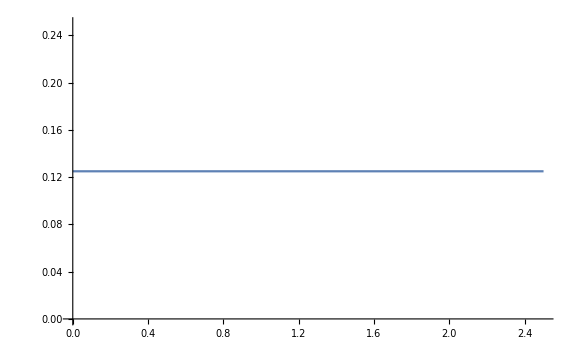

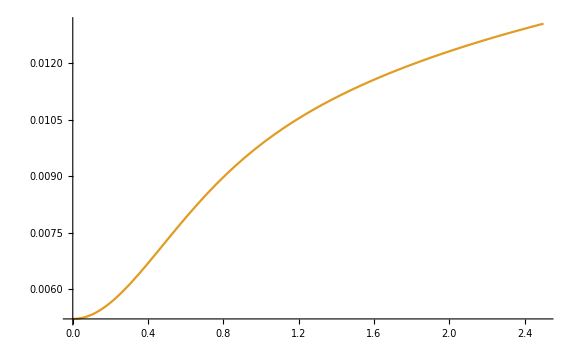

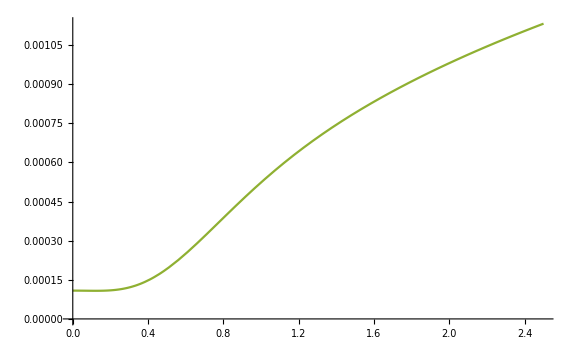

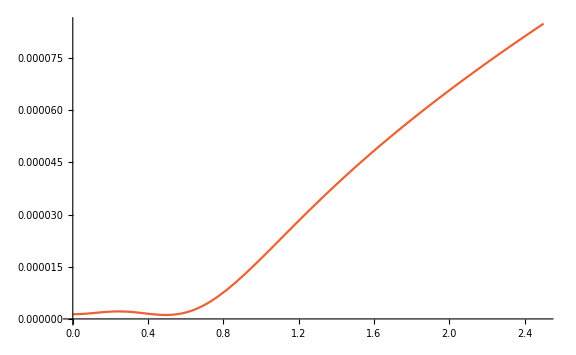

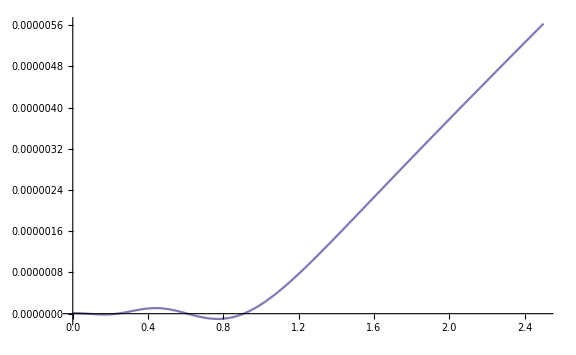

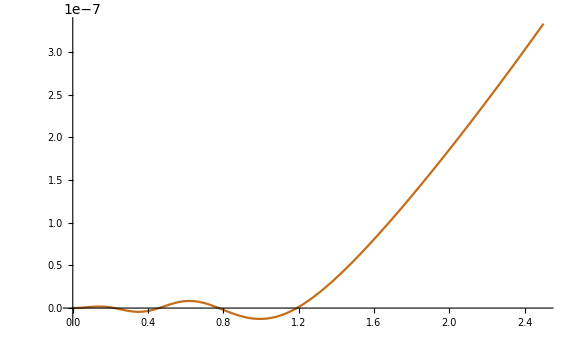

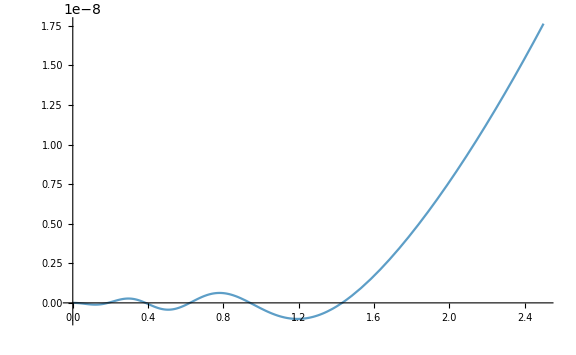

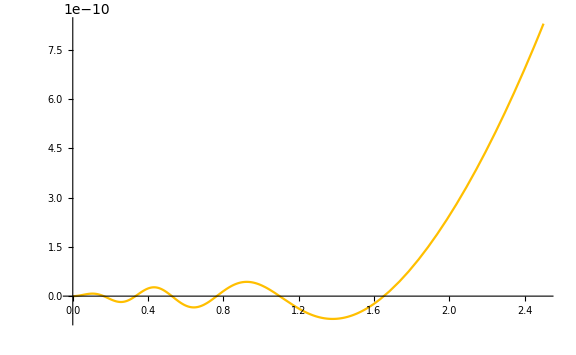

```mathematica
For[ll=1,ll<=10,ll++,
Print[Plot[tmp4[[ll]],{M,0,2.5},AxesLabel->{MaTeX["M"],MaTeX["\\frac{\\mathbb{W}_{\\ell}(2\\pi)}{\\left. \\mathbb{W}_{\\ell}(2\\pi) \\right|_{M=0}}"],Black},PlotStyle->defaultplotstyle[[ll]],PlotLegends->Row[{MaTeX["\\ell = "],ll}],ImageSize->Large]];
];

Clear[ll]
```

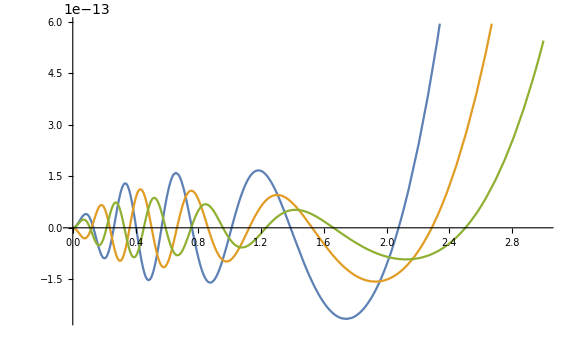

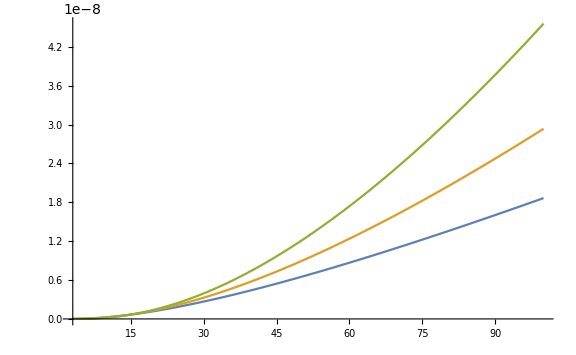

```mathematica
{tmp4[[10]],10tmp4[[11]],100tmp4[[12]]};

Plot[Evaluate@%,{M,0,3},AxesLabel->{MaTeX["M"],"",Black},PlotStyle->defaultplotstyle,PlotLegends->{MaTeX["\\mathbb{W}_{10}(2\\pi)"],MaTeX["10\, \\mathbb{W}_{11}(2\\pi)"],MaTeX["100\, \\mathbb{W}_{12}(2\\pi)"]},ImageSize->Large]

Plot[Evaluate@%%,{M,3,100},AxesLabel->{MaTeX["M"],"",Black},PlotStyle->defaultplotstyle,PlotLegends->{MaTeX["\\mathbb{W}_{10}(2\\pi)"],MaTeX["10\, \\mathbb{W}_{11}(2\\pi)"],MaTeX["100\, \\mathbb{W}_{12}(2\\pi)"]},ImageSize->Large]

Clear[ll]
```

## Padé approximants - finite M

```mathematica
(* strong-coupling formula 1408.6040 *)

WLargeCoupling[λ_,M_,cutoffSum_]:=Module[{μ,ϕ,ghat},
μ=(√(λ(1+M^2)))/(2π);
ϕ=2M ArcTan[M]-Log[M^2+1];
ghat[ω_]:=(ⅈ^(3/2)√π)/(2ω √ω)((M^2 Sinh[ω/2]^2-Sin[(M ω)/2]^2)/(Sinh[ω/2]^2+Sin[(M ω)/2]^2)+(M^2+1)^2 ω Exp[-(ⅈ ϕ ω)/(2π)](Gamma[(M-ⅈ)/(2π)ω]Gamma[-(M+ⅈ)/(2π)ω])/Gamma[-(ⅈ ω)/(2π)]^2 Total[Table[(-1)^n/(n n!)(Exp[(ⅈ ϕ n)/(M-ⅈ)]/(ω-(2π n)/(M-ⅈ))Gamma[(M+ⅈ)/(M-ⅈ)n]/Gamma[ⅈ/(M-ⅈ)n]^2+Exp[-(ⅈ ϕ n)/(M+ⅈ)]/(ω+(2π n)/(M+ⅈ))Gamma[(M-ⅈ)/(M+ⅈ)n]/Gamma[-ⅈ/(M+ⅈ)n]^2),{n,cutoffSum}]]);
2^(3/2)/(π μ^(3/2))Exp[2π μ](If[M===0,0,ghat[2π ⅈ]]+1/(2^(5/2)π))
]
```

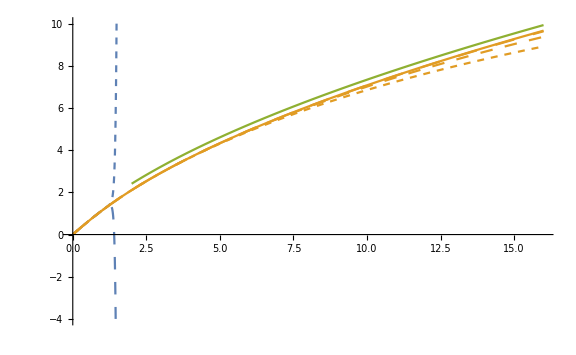

```mathematica
(* plot *)

prec=50;
M=SetPrecision[0.5,prec];
If[cutoffλ>=35,Last[{

(* series of Log[W̃[x]] *)
Monitor[
bucket=Sum[λ^ll Wλ[x,ll]/.solution/.{Derivative[n_][γ][0]:>γExpl[n]},{ll,0,35}],
Row[{ProgressIndicator[ll,{1,cutoffλ}],""},Row[{" Evaluate order λ: ",ll,"/",cutoffλ}]]];
bucket=Series[Log[bucket],{λ,0,35}];
Monitor[
Table[logWλ[x_,ll]=SeriesCoefficient[bucket,ll],{ll,0,35}]//Simplify,
Row[{ProgressIndicator[ll,{1,cutoffλ}],""},Row[{" Evaluate order λ: ",ll,"/",cutoffλ}]]];

(* approximants *)
pol[λ_,n_]:=Sum[logWλ[1,ll] λ^ll,{ll,0,n}];
pade[5,λ_]=PadeApproximant[pol[λ,35],{λ,0,5}]//Simplify;
pade[9,λ_]=PadeApproximant[pol[λ,35],{λ,0,9}]//Simplify;
pade[13,λ_]=PadeApproximant[pol[λ,35],{λ,0,13}]//Simplify;
pade[17,λ_]=PadeApproximant[pol[λ,35],{λ,0,17}]//Simplify;

cutoffSum=20;
Plot[Evaluate@Flatten[{{pol[π^2 λOverPi2,34]}, {pol[π^2 λOverPi2,35]}, {pade[5,π^2 λOverPi2]}, {pade[9,π^2 λOverPi2]}, {pade[13,π^2 λOverPi2]}, {pade[17,π^2 λOverPi2]}, {If[λOverPi2>2,Log[WLargeCoupling[π^2 λOverPi2,M,cutoffSum]]]}}],{λOverPi2 ,0,16},PlotRange->{-4,10},AxesLabel->{MaTeX["\\lambda/{\\pi^2}"],"",Black},PlotStyle->Flatten[{{{defaultplotstyle[[1]],Dashing[Small]}}, {{defaultplotstyle[[1]],Dashing[Medium]}}, {{defaultplotstyle[[2]],Dashing[Small]}}, {{defaultplotstyle[[2]],Dashing[Medium]}}, {{defaultplotstyle[[2]],Dashing[Large]}}, {defaultplotstyle[[2]]}, {defaultplotstyle[[3]]}},1],PlotLegends->Flatten[{{MaTeX["\\mathbb{W}_{(34)}(2\\pi)"]}, {MaTeX["\\mathbb{W}_{(35)}(2\\pi)"]}, {MaTeX["[5/5]"]}, {MaTeX["[9/9]"]}, {MaTeX["[13/13]"]}, {MaTeX["[17/17]"]}, {MaTeX["\\textrm{Strong coupling}"]}}],ImageSize->Large]

}]]

Clear[prec,M,ll,bucket,logWλ,pol,pade,cutoffSum]
```

## Taylor coefficients - large M

```mathematica
If[cutoffλ>=20,{

tmp5=Table[0,{ll,20}];
SetSharedVariable[tmp5];
ParallelTable[{
Print[" Expand order λ: ",ll,"/",20];

bucket=tmp4[[ll]];

If[Head[bucket]===Plus,bucket=List@@bucket,bucket={bucket}];
Print[tmp4[[ll]]==Total[bucket]];

bucket=Series[bucket,{M,∞,0}]//FunctionExpand//Total;
bucket=Collect[bucket,Log[M],Simplify];
tmp5[[ll]]=Series[bucket,{M,∞,0}];
},{ll,20},Method->"FinestGrained"];

}];

Join[{tmp5[[1]]//Normal},Table[Coefficient[tmp5[[ll]]//Normal,Log[M]^(ll-1)],{ll,2,10}]]==Table[1/(8(4 π^2)^(ll-1)),{ll,10}]//Simplify
Clear[bucket,ll]
```

Expand order λ: 1/20

Expand order λ: 2/20

True

True

Expand order λ: 3/20

True

Expand order λ: 4/20

Expand order λ: 5/20

True

True

Expand order λ: 6/20

True

Expand order λ: 7/20

True

Expand order λ: 8/20

True

Expand order λ: 9/20

True

Expand order λ: 10/20

True

Expand order λ: 11/20

True

Expand order λ: 12/20

True

Expand order λ: 13/20

True

Expand order λ: 14/20

True

Expand order λ: 15/20

True

Expand order λ: 16/20

True

Expand order λ: 17/20

True

Expand order λ: 18/20

True

Expand order λ: 19/20

True

Expand order λ: 20/20

True

True

## Save/load

```mathematica
(* Save[NotebookDirectory[]<>"Solver N=2star SYM analytic (cont).mx","Global`"]; *)
```

```mathematica
(* <<(NotebookDirectory[]<>"Solver N=2star SYM analytic (cont).mx"); *)
```